# Adaptive Introgression Generating Function Functions

Here we model adaptive introgression after secondary contact ussing the model of Setter et al 2020. For analysis,  we parameterize the generating function as a sequence of demographic events backward in time, measuring the time interval between successive vents.  However, for many applications, we often assume that the species split at some fixed time Ts (s for split) in the past and that adaptive introgression occurs at some time 0 <= Ta <= Ts.  Measuring the inter-event times, the first event is adaptive introgression  ocurring after a time interval Ta.  The second event is the subsequent split occurring after a second interval of length Ts-Ta.

## Neutral Coalescent

### Helper Functions

```mathematica
TakeAway::usage = "TakeAway[U,V]  gives the set U, minus elements V. Note that this is not the same as Complement[U,V] if U contains repeated elements. ";
```

```mathematica
TakeAway[U_List, {}] := U;
(*TakeAway[U_List,{{}}]:=If[MemberQ[U,{{}}],TakeAway[U,{{}}],U];*)
TakeAway[U_List, {v_}] := Drop[U, Cases[Position[U, v],{_Integer}]⟦1⟧] /; Complement[{v}, U] == {};
TakeAway[U_List, V_List] := TakeAway[TakeAway[U, Take[V, 1]], Drop[V, 1]] /; Complement[V, U] == {};
TakeAway[U_List, W__List, V_List] := TakeAway[TakeAway[U, W], V];
```

```mathematica
GetVars::usage="GetVars[expr,ψ] lists the configurations of genes in all terms of the form ψ[ω,genes,options], GetVars[{expr,…},ψ] lists all the variables.";
```

```mathematica
GetVars[expr_,GF_]:=Cases[Variables[GF],expr[_]];
```

```mathematica
(*functions to convert the {a+b+c} notation for the i-Ton branch recursion to the {a,b,c} notation for the fully-labelled topology as described in the manuscript*)Listify[yl_List]:=Block[{x = yl[[1]]},
If[Length[x]==0,{x},x[[0]]=List;x]
];ConvertNotation[expr_,ω_]:=expr/.ω[x_]:>   ω[Listify[x]];
```

### Recursion

```mathematica
MakeCoalEvents[xl_List]:=Module[
{myTupleRates = Tally[Subsets[Sort[xl],{2}]],
yl},
yl = {#⟦2⟧,Append[TakeAway[xl,#⟦1⟧],List[Total[Flatten[#⟦1⟧]]]]}&/@myTupleRates
];

GFn[ω_,xl_List]:=Module[{coalList = MakeCoalEvents[xl],λ=Binomial[Length[xl],2]},
If[Length[xl]==1,1,
1/(λ+Total[ω[#]&/@xl])*Total[( #⟦1⟧ * GFn[ω,#⟦2⟧])&/@coalList]
]
];
```

### Secondary Contact

```mathematica
GFsplit[ω_,pL_List,ϵ_]:=Module[
{xdL =First[pL],xrL = Last[pL],coalList,
allEvents,totalRates},

coalList = MakeCoalEvents[xrL];
totalRates = Total[#⟦1⟧&/@coalList]+ϵ;

If[Total[Length[#]&/@pL]≤1,1,
1/(totalRates+Total[ω[#]&/@xrL]+Total[ω[#]&/@xdL])*
( Total[( #⟦1⟧ * GFsplit[ω,{xdL,#⟦2⟧},ϵ])&/@coalList]+ϵ GFn[ω,Join[xdL,xrL]])
]

];
```

## Starlike Approximation

### Recursion

```mathematica
Pe[k_,n_,alpha_]:=Module[
{Pesc = 1 - Exp[-alpha]},
Binomial[n,k]*Pesc^k*(1-Pesc)^(n-k);
(*If[k==0,(1 - Sum[P[j,n],{j,1,n}]),
P[k,n]]*)
P[k,n]
]
```

```mathematica
PknToAlpha[k_,n_]:=Module[
{Pesc = 1 - Exp[-α]},
Binomial[n,k]*Pesc^k(1-Pesc)^(n-k)
];
```

```mathematica
MakeAiStarlikeEvents[xl_List,delta_,alpha_]:=Module[
{myTupleRates,n=Length[xl],numTuples,
yl,returnList={}
},
For[k=0,k<n,k++,
myTupleRates = Tally[Subsets[Sort[xl],{n-k}]];
numTuples =Total[#[[2]]&/@myTupleRates];(* Length[myTupleRates];*)
(*yl = {delta*Pe[k,n,alpha]*1/numTuples,
Append[TakeAway[xl,#⟦1⟧],List[Total[Flatten[#⟦1⟧]]]]}&/@myTupleRates;*)
yl = {delta*Pe[k,n,alpha]*#[[2]]/numTuples,{{List[Total[Flatten[#⟦1⟧]]]},TakeAway[xl,#⟦1⟧]}}&/@myTupleRates;

returnList = Join[returnList,yl];
];
(*for k = n separate to avoid adding empty {} lineage to branch set*)
yl = {{delta*Pe[n,n,alpha]*1,{{},xl} }};
returnList = Join[returnList,yl];
returnList = Flatten[returnList,0];
Return[returnList]
]
```

```mathematica
GFaiStar[alpha_,ω_,xl_List,δa_,δs_]:=Module[
{coalList = MakeCoalEvents[xl],starList = MakeAiStarlikeEvents[xl,δa,alpha],allEvents,totalRates},


totalRates = Total[#[[1]]&/@coalList]+Total[#[[1]] &/@ starList];

If[Length[xl]==1,1,
1/(totalRates+Total[ω[#]&/@xl])*(
Total[( #⟦1⟧ * GFaiStar[alpha,ω,#⟦2⟧,δa,δs])&/@coalList]+
Total[(#⟦1⟧*GFsplit[ω,#⟦2⟧,δs])&/@starList]
)
]
];
```

### Simplification Functions

```mathematica
subAllPeeToOne[n_]:=Table[
Sum[ P[i,k],{i,0,k}]-> 1,
{k,1,n}];
subAllPeeToEpsilon[n_]:=Table[
Sum[ ϵ_ P[i,k],{i,0,k}]-> ϵ,
{k,1,n}];
subPeeToOneMinus[n_]:=Block[
{part,
res=List[],
allVals, currentVals
},
For[k=2,k≤n,k++,
allVals = Table[ii,{ii,0,k}];
For[x=0,x≤k,x++,
currentVals=DeleteCases[allVals,x];
part = Sum[P[i,k],{i,currentVals}]-> 1 - P[x,k];
res = Append[res,part];
];
];
res
];
subPeeToEpsilonMinus[n_]:=Block[
{part,
res=List[],
allVals, currentVals
},
For[k=2,k≤n,k++,
allVals = Table[ii,{ii,0,k}];
For[x=0,x≤k,x++,
currentVals=DeleteCases[allVals,x];
part = Sum[ ϵ_ P[i,k],{i,currentVals}]-> ϵ( 1 - P[x,k]);
res = Append[res,part];
];
];
res
];

SubSimplifyPeeRulesv2[expr_,n_]:=Block[
{thisExp = ReleaseHold[expr],
nextExp,
subIntPos = i_Integer P[s__]:> HoldForm[(i-1)P[s]] +P[s]/;i>1,
subIntNeg = i_Integer P[s__]:> HoldForm[(i+1)P[s]] -P[s]/;i<-1,
a},

While[True,

nextExp = thisExp//.subIntPos//.subIntNeg;
nextExp = thisExp//.subIntPos//.subIntNeg;
nextExp = nextExp//.subAllPeeToOne[n]//.subAllPeeToEpsilon[n]//.subPeeToOneMinus[n]//.subPeeToEpsilonMinus[n];
nextExp = nextExp//.subAllPeeToOne[n]//.subAllPeeToEpsilon[n]//.subPeeToOneMinus[n]//.subPeeToEpsilonMinus[n];
nextExp = ReleaseHold[nextExp];
a = thisExp -nextExp;

If[a==0,Break[],Print["no"]];
thisExp = nextExp

];
thisExp = thisExp ;(*//.subPeeToOneMinus[n]//.subPeeToEpsilonMinus[n];*)
Return[thisExp]
];
```

### functions to get means, pdfs, cdfs for marginals T1, T2, T3,...

```mathematica
GetGfAsList[n_,gfExpr_]:=Block[{doIfTrue,doIfFalse,sample = Table[{1},{i,1,n}]},
doIfFalse[]:=Block[{},Print["n <= 2"];Return[Return["False"]]];
doIfTrue[]:=Block[
{gf,peeTable,subPSums,deltaPeeTable,subDeltaPeeSums},

gf = Expand[gfExpr];
gf⟦0⟧= List;
gf =SubSimplifyPeeRulesv2[#,n]&/@ gf //Parallelize;
gf
];
If[n> 2,doIfTrue[],doIfFalse[]]
];
```

```mathematica
MakeMeanList[gfDelta_List,n_,ω_,t_,δa_,Ta_,δs_,Ts_]:=Block[
{
means = {},
xs,
subTable,
steps
},
steps[pathGF_,ii_]:=Block[{pgf},
pgf = (-1)D[pathGF,ω[{ii}]];
pgf = pgf/.subTable;
pgf =  InverseLaplaceTransform[pgf/δa,δa,Ta];
pgf =  InverseLaplaceTransform[pgf/δs,δs,Ts];
pgf
];
subTable = ω[{#}]->0&/@Table[j,{j,1,n}]; (*all sub to zero here*)
For[i = 1, i<n,i++,
xs = steps[#,i]&/@gfDelta //Parallelize;
means = Append[means,xs];
];
means = Total[#]&/@ means;
Return[means]
]
```

```mathematica
MakePDFList[gfDelta_List,n_,ω_,t_,δa_,Ta_,δs_,Ts_]:=Block[
{
marginals={},
xs,
subTable,
steps
},

steps[pathGF_,ii_,sTab_]:=Block[{pgf},
pgf = pathGF/.sTab;
pgf =  InverseLaplaceTransform[pgf/δa,δa,Ta];
pgf =  InverseLaplaceTransform[pgf/δs,δs,Ts];
pgf = InverseLaplaceTransform[pgf,ω[{ii}],t]
];

For[i=1,i<n,i++,
subTable = DeleteCases[Table[j,{j,1,n}],i];
subTable = ω[{#}]->0&/@subTable;

xs = steps[#,i,subTable]&/@gfDelta //Parallelize;

marginals = Append[marginals,xs];
];
marginals = Total[#]&/@marginals;
Return[marginals]
]
```

```mathematica
MakeCDFList[gfDelta_List,n_,ω_,t_,δa_,Ta_,δs_,Ts_]:=Block[
{
marginals={},
xs,
subTable,
steps
},

steps[pathGF_,ii_,sTab_]:=Block[{pgf},
pgf = pathGF/.sTab;
pgf =  InverseLaplaceTransform[pgf/δa,δa,Ta];
pgf =  InverseLaplaceTransform[pgf/δs,δs,Ts];
pgf = InverseLaplaceTransform[pgf/ω[{ii}],ω[{ii}],t]
];

For[i=1,i<n,i++,
subTable = DeleteCases[Table[j,{j,1,n}],i];
subTable = ω[{#}]->0&/@subTable;

xs = steps[#,i,subTable]&/@gfDelta //Parallelize;

marginals = Append[marginals,xs];
];
marginals = Total[#]&/@marginals;
Return[marginals]
]
```

```mathematica
(*This takes the list of marginal pdfs and cdfs. For each marginal (1-ton, 2-ton etc.), it determines the discontinuities (heavisides and diracdeltas) present. From these, we want to determine the size of the point masses.  I was previously checking every discontinuity, just in case. That's too expensive. And it's dumb.  DiracDelta terms tell us there's a pointmass. So now I'm only looking at those. 

The return is a list of 
{i-ton type, {discontinuities}, {point masses}}
	The point masses are described as {T-Td,val} where T_d is the discontinuitiy (was easy, could be modified to show T-> Td instead. If it returns {T,val}, the pointmass is located at 0.
*)
MakeALim[exp_Symbol,T_]:={T-> 0};
MakeALim[exp_Plus,T_]:={T-> T-exp};

FromTheLeft[exp_,lim_]:=If[Cases[Values[lim],0 ]≠ {},0,Limit[exp,lim,Direction->"FromBelow"]];
FromTheRight[exp_,lim_]:=Limit[exp,lim,Direction->"FromAbove"];

GetJumps[spL_List,scL_List,T_]:=Block[{ret,thisRes,disconts,diracDisconts,limits,leftLims,rightLims,jumpSizes},
ret = {};
For[i=1,i≤Length[spL],i++,
thisRes = {i};
(*Print[i];*)
disconts = DeleteDuplicates[Cases[spL⟦i⟧,HeavisideTheta[_]|DiracDelta[_],Infinity]];
thisRes = thisRes ~Append~disconts;
diracDisconts = Cases[disconts,DiracDelta[_],Infinity]; 
(*Print[diracDisconts];*)
If[Length[diracDisconts] == 0,diracDisconts={diracDisconts},None];
(*Print[diracDisconts];*)
diracDisconts=diracDisconts/.{DiracDelta[ζ_]->ζ} ;
(*Print[diracDisconts];*)
diracDisconts = DeleteDuplicates[diracDisconts];
limits = MakeALim[#,T]&/@diracDisconts;
(*Print[limits];*)
leftLims = FromTheLeft[scL⟦i⟧,#]&/@limits;
rightLims = FromTheRight[scL⟦i⟧,#]&/@limits;
(*Print[leftLims];
Print[rightLims];*)
jumpSizes =MapThread[FullSimplify[(#1 - #2)/.HeavisideTheta[_]->0]&,{rightLims,leftLims}];
jumpSizes = FullSimplify[ SubSimplifyPeeRulesv2[#,4]]&/@jumpSizes;
thisRes = Append[thisRes,MapThread[{#1,#2}&,{diracDisconts,jumpSizes}]];
(*thisRes = MapThread[{{i,#1},#2}&,{diracDisconts,jumpSizes}];*)
(*ret = Append[ret,thisRes];*)
ret = Append[ret, thisRes];
];
ret
]

MakePiecewise[expression_,t_,assums_]:= Module[{expr,disconts,left,right,intervals,assumptions,piecewise},
(*disconts = DeleteDuplicates[Cases[expr,HeavisideTheta[_]|DiracDelta[_],Infinity]];*)
expr = Assuming[ assums,FullSimplify[expression]];
(*Print[expr];*)
disconts = DeleteDuplicates[Cases[expr,HeavisideTheta[_]|DiracDelta[_],Infinity]];
(*Print[disconts];*)
If[disconts=={},Return[{{expr,0≤ t<Infinity }}]];
disconts = (t-#/.p_[x_]:> x) &/@disconts;
disconts= DeleteDuplicates[{0} ~Join~ disconts~Join~{Infinity}]//Sort;
left = disconts[[1;;-2]];
right = disconts[[2;;-1]];
assumptions =MapThread[ #1≤    t<   #2&,{left,right}] ;
(*Print[assumptions];*)
piecewise = Assuming[ assums && #,FullSimplify[expr/.HeavisideTheta->UnitStep]]&/@assumptions  ;
piecewise = SubSimplifyPeeRulesv2[Expand[#],4]&/@piecewise//FullSimplify;
MapThread[{#2,assums &&  #1}&,{assumptions,piecewise}]
];
```

## Instant Yule Approximation

### Partition probabilities

```mathematica
PFi[n_,i_]:= ∏_(j=1)^(n-1) (i-j)/(i+j)(*i number of lineages in big yule tree, n lineages in sample*)
pnotrec[f_,r_,s_,Ne_,M_]:= ⅇ^(-(r/s*∑_(i=f)^M 1/i))(*probability of no recombination *)

m[s_,r_,n_]:=Max[1,(r*n)/s*∑_(i=1)^(n-1) 1/i](*correction factor*)


(*E=size of early recombinant family, L = number of late recombining singletons, n=sample size, n-E-L=number of lineages that did not escape*)
Clear[PELN];
PELN[E_, L_, n_, s_, r_,Ne_,M_]:=PELN[E,L,n,s,r,Ne,M]=Module[
{pfisf,pnorec,prec, ExpectPf, correctionF = m[s,r,n]},
(*probability P(F=f), subtract P(F≤i+1)-P(F≤i) = PFi[i+1]-PFi[i]*)
pfisf = Differences[PFi[n,#]&/@Range[n-1,M]];
pnorec = pnotrec[#,r,s,Ne,M]&/@Range[n,M];
(*pnorec=p[#,r,s,Ne]&/@Range[n,M];*)
prec = 1-pnorec;
ExpectPf = Total[pnorec^(n-L)*prec^L*pfisf];
	If[E≥2,ExpectPf* (r*n)/(s*correctionF)*1/(E(E-1))((n-1)*Binomial[n-2,E-2]*Boole[L+E==n]+Binomial[n-1,L]),
If[E==1,ExpectPf*(r*n)/(s*correctionF)*(Boole[L+1==n]+Binomial[n-1,L]*∑_(i=2)^(n-1) 1/i+∑_(S=2)^n Binomial[n-S, L-S+1]/(S-1)),
If[correctionF>1,ExpectPf*(Max[0,Binomial[n,L](1-correctionF)]+(r*n)/(s*correctionF)(1/n*Boole[L==n]+Binomial[n-1,L-1]*∑_(i=2)^(n-1) 1/i+∑_(S=2)^n Binomial[n-S,n-L]*1/(S(S-1)))),
ExpectPf*(Binomial[n,L](1-(r*n)/s(∑_(i=1)^(n-1) 1/i-L/n∑_(i=2)^(n-1) 1/i))+(r*n)/s(1/n*Boole[L==n]+∑_(S=2)^n Binomial[n-S,n-L]*1/(S(S-1))))]]]

];
```

### Helper Functions For GF recrusion for yule approximation

```mathematica
(*gives the number of ways to divide n into 3 buckets, including empty bucket*)
partitions[X_]:=Catenate[Permutations/@IntegerPartitions[X,{3},Range[0,X]]];
(*given the types of partitions, make all combinations for our sample, and calculate probability of this configuration. returns (partition, probability, sample_configuration following coalescence). Hold is used to avoid having to specify all parameters prior to taking inverse laplace transforms.*)
part3[a_List,p_List,s_,r_,Ne_,M_]:=Module[{f,sym,prob,result},Attributes[f]=Orderless;
(*prob=PELN[p[[1]],p[[2]],Total[p],s,r, Ne,M];*)
(*prob=Peln[p[[1]],p[[2]],Total[p]];*)
prob=Peln[p[[1]],p[[2]],Total[p],s,r,Ne,M];
sym=Unique["x",Temporary]&/@p;
result=ReplaceList[f@@a,f@@MapThread[Pattern[#,Repeated[_,{#2}]]&,{sym,p}]->{p,prob,List/@sym}];
Return[result]
];

sumelms[a_List]:=Module[{E,nonrec, rec},
E = If[Length[a[[3,1]]]==0,{},Total[a[[3,1]]]];
nonrec=If[Length[a[[3,3]]]==0,{},Total[a[[3,3]]]];
rec=Sort[DeleteCases[Join[List[E],a[[3,2]]],{}]];
{a[[1]],a[[2]],List[rec,DeleteCases[List[nonrec],{}]]}];
```

### Recursion

```mathematica
MakeYulelikeEvents[xl_List,delta_,s_,r_,Ne_,M_]:=Module[
{allFamilies,Counts,CountsAssociation,countFamilies,n=Length[xl]
},
allFamilies=Flatten[part3[xl,#,s,r,Ne,M]&/@partitions[n],1];
allFamilies=sumelms/@allFamilies;
Counts = Tally[allFamilies[[All,1]]];
CountsAssociation = AssociationThread[Counts[[All,1]],Counts[[All,2]]];
allFamilies=List[delta*(#[[2]])/CountsAssociation[#[[1]]],#[[3]]]&/@allFamilies;
countFamilies = Tally[allFamilies];
allFamilies=List[#[[1,1]]*#[[2]],#[[1,2]]]&/@countFamilies;
Return[allFamilies]
]

GFaiYule[s_,r_,Ne_,M_,ω_,xl_List,dl_List]:=Module[
{coalList = MakeCoalEvents[xl],YuleList = MakeYulelikeEvents[xl,dl⟦1⟧,s,r,Ne,M],allEvents,totalRates,ϵ=dl⟦2⟧},
(*ϵ here is dummy var for split time. should it be included here or only in later parts of the recursion?*)
totalRates = Total[#[[1]]&/@coalList]+Total[#[[1]] &/@ YuleList];

If[Length[xl]==1,1,
1/(totalRates+Total[ω[#]&/@xl])*(
Total[( #⟦1⟧ * GFaiYule[s,r,Ne,M,ω,#⟦2⟧,dl])&/@coalList]+
Total[(#⟦1⟧*GFsplit[ω,Reverse@#⟦2⟧,ϵ])&/@YuleList]
)
]
];
```

### Marginal PDFs and CDFs

```mathematica
MakeMargeList[gfDelta_List,sample_,ω_,t_,δ_,Td_, ϵ_,Te_]:=Module[
{n = Length[sample],
marginals={},
xs,
subTable
},
For[i=1,i<n,i++,
subTable = DeleteCases[Table[j,{j,1,n}],i];
subTable = ω[{#}]->0&/@subTable//Parallelize;
xs = #/.subTable &/@gfDelta//Parallelize;
xs = InverseLaplaceTransform[1/δ  #,δ,Td]&/@xs//Parallelize;
xs = InverseLaplaceTransform[1/ϵ #,ϵ,Te]&/@xs//Parallelize;
xs = InverseLaplaceTransform[#,ω[{i}],t]&/@xs//Parallelize;
marginals = Append[marginals,xs];
];
Return[marginals]
]
```

```mathematica
MakeCumuList[gfDelta_List,sample_,ω_,t_,δ_,Td_, ϵ_,Te_]:=Module[
{n = Length[sample],
marginals={},
xs,
subTable
},
For[i=1,i<n,i++,
subTable = DeleteCases[Table[j,{j,1,n}],i];
subTable = ω[{#}]->0&/@subTable//Parallelize;
xs = #/.subTable &/@gfDelta//Parallelize;
xs = InverseLaplaceTransform[1/δ  #,δ,Td]&/@xs//Parallelize;
xs = InverseLaplaceTransform[1/ϵ #,ϵ,Te]&/@xs//Parallelize;
xs = InverseLaplaceTransform[#/ω[{i}],ω[{i}],t]&/@xs//Parallelize;
marginals = Append[marginals,xs];
];
Return[marginals]
]
```

## Functions for Data

```mathematica
MakeDataArray[Ts_,dataFile_,shape_,datNe_]:= Module[
{
data = BinaryReadList[dataFile,"Real32"],reshape,reshapeTranspose,margTable
},
reshape = ArrayReshape[data,shape];
reshapeTranspose = Transpose[reshape];
margTable = Table[
 {(j-1),
Table[#[[i]]/(2*datNe)&/@reshapeTranspose[[j]],{i,1,3,1}]}
,{j,1,Length[reshapeTranspose]}]
]
```

# Results

## n=2

### AI. starlike only. gf function for n = 2 and expected time to MRCA

```mathematica
gfDeltaEpsilon = GFaiStar[α,ω,{{1},{1}},δa,δs];
gfDeltaEpsilon
gfTaEpsilon = InverseLaplaceTransform[ gfDeltaEpsilon /δa,δa,Ta];
gfTaTs = InverseLaplaceTransform[gfTaEpsilon/δs,δs,Ts];
SubSimplifyPeeRulesv2[gfTaTs,2]
```

(1+δa P[0,2]+(δa δs P[1,2])/((1+2 ω[{1}]) (δs+2 ω[{1}]))+(δa P[2,2] (1+δs/(1+2 ω[{1}])))/(1+δs+2 ω[{1}]))/(1+δa P[0,2]+δa P[1,2]+δa P[2,2]+2 ω[{1}])

(ⅇ^(Ta (-1-2 ω[{1}])-2 Ts ω[{1}]) P[1,2])/(1+2 ω[{1}])+(1-ⅇ^(Ta (-1-2 ω[{1}])) P[1,2]+2 ⅇ^(Ta (-1-2 ω[{1}])) P[0,2] ω[{1}])/(1+2 ω[{1}])

```mathematica
TmrcaAI[α_,Ta_,Ts_]=1/2*(-1*D[gfTaTs,ω[{1}]]/.ω[_]->0/.P->PknToAlpha);
Print["Expected Total Singleton Branch Length"];
SubSimplifyPeeRulesv2[-1*D[gfTaTs,ω[{1}]]/.ω[_]->0,2]/2//FullSimplify
With[{TaIncrement = .25,Ts=4.0},
Plot[
Evaluate[Table[
TmrcaAI[α,TaIncrement*i,Ts+TaIncrement*i],{i,0,8}]],{α,0,6},PlotRange->All]
]
```

Expected Total Singleton Branch Length

ⅇ^-Ta (ⅇ^Ta-P[0,2]+Ts P[1,2])

We recover the  ‘Volcano’ pattern in pairwise genetic diversity described in Setter et al 2020: the loss of diversity is observed only very near the sweep center, and this valley of diversity narrows as the divergence of the donor increases. In contrast,  diversity is increased in the flanking regions by an amount proportional to the divergence of the donor.   As the time since the sweep increases,  diversity recovers to background levels.

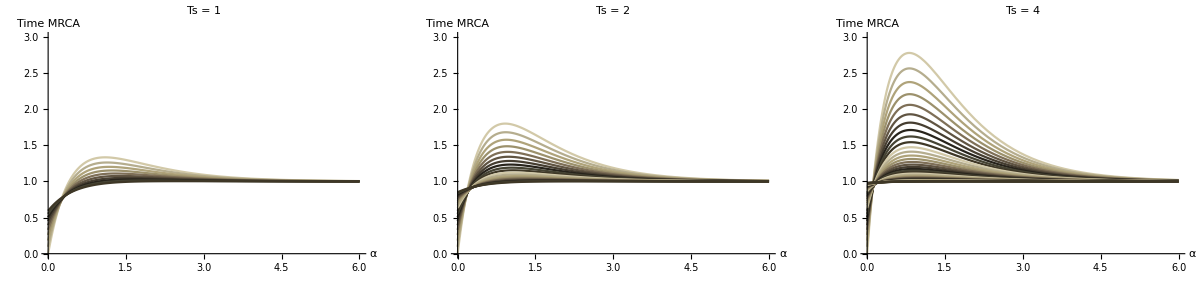

```mathematica
GraphicsRow[
{
With[{TaIncrement = .1,Ts=1},
numVals = -1+Ts/TaIncrement//Floor;
If[numVals<1,numVals=0];
taList = Table[TaIncrement*i,{i,0,numVals}];
LegendItems = ToString/@taList;
LegendItems = "Ta = "<>#&/@LegendItems;
Plot[
Evaluate[Table[
TmrcaAI[α,TaIncrement*i,Ts-TaIncrement*i],{i,0,numVals}]],{α,0,6},PlotRange->{All,{0,3}},PlotStyle->ColorData[49],(*PlotLegends->SwatchLegend[LegendItems],*)PlotLabel->"Ts = "<>ToString[Ts],AxesLabel->{"α","Time MRCA"},AxesStyle->Bold]
],
With[{TaIncrement = .1,Ts=2},
numVals = -1+Ts/TaIncrement//Floor;
If[numVals<1,numVals=0];
taList = Table[TaIncrement*i,{i,0,numVals}];
LegendItems = ToString/@taList;
LegendItems = "Ta = "<>#&/@LegendItems;
Plot[
Evaluate[Table[
TmrcaAI[α,TaIncrement*i,Ts-TaIncrement*i],{i,0,numVals}]],{α,0,6},PlotRange->{All,{0,3}},PlotStyle->ColorData[49],(*PlotLegends->SwatchLegend[LegendItems],*)PlotLabel->"Ts = "<>ToString[Ts],AxesLabel->{"α","Time MRCA"},AxesStyle->Bold]
],
With[{TaIncrement = .1,Ts=4},
numVals = -1+Ts/TaIncrement//Floor;
If[numVals<1,numVals=0];
taList = Table[TaIncrement*i,{i,0,numVals}];
LegendItems = ToString/@taList;
LegendItems = "Ta = "<>#&/@LegendItems;
Plot[
Evaluate[Table[
TmrcaAI[α,TaIncrement*i,Ts-TaIncrement*i],{i,0,numVals}]],{α,0,6},PlotRange->{All,{0,3}},PlotStyle->ColorData[49],(*PlotLegends->SwatchLegend[LegendItems]*)PlotLabel->"Ts = "<>ToString[Ts],AxesLabel->{"α","Time MRCA"},AxesStyle->Bold]
]
},
ImageSize->Full
]
```

### Marginal Distributions for n = 2

```mathematica
gfDeltaEpsilon = GFaiStar[α,ω,{{1},{1}},δa,δs];
selGFList = gfDeltaEpsilon //Expand; selGFList[[0]] = List;
selGFList
```

{1/(1+δa P[0,2]+δa P[1,2]+δa P[2,2]+2 ω[{1}]),(δa P[0,2])/(1+δa P[0,2]+δa P[1,2]+δa P[2,2]+2 ω[{1}]),(δa δs P[1,2])/((1+2 ω[{1}]) (δs+2 ω[{1}]) (1+δa P[0,2]+δa P[1,2]+δa P[2,2]+2 ω[{1}])),(δa P[2,2])/((1+δs+2 ω[{1}]) (1+δa P[0,2]+δa P[1,2]+δa P[2,2]+2 ω[{1}])),(δa δs P[2,2])/((1+2 ω[{1}]) (1+δs+2 ω[{1}]) (1+δa P[0,2]+δa P[1,2]+δa P[2,2]+2 ω[{1}]))}

```mathematica
smList = FullSimplify[SubSimplifyPeeRulesv2[#,2]]&/@ MakeMeanList[selGFList,2,ω,t,δa,Ta,δs,Ts];
spList =  FullSimplify[SubSimplifyPeeRulesv2[#,2]]&/@MakePDFList[selGFList,2,ω,t,δa,Ta,δs,Ts];
scList =  FullSimplify[SubSimplifyPeeRulesv2[#,2]]&/@MakeCDFList[selGFList,2,ω,t,δa,Ta,δs,Ts];
```

```mathematica
fT1[t_,Ta_,Ts_,α_] = spList[[1]] /.P->PknToAlpha;
FT1[t_,Ta_,Ts_,α_] = scList[[1]]/.P->PknToAlpha;
```

For the distribution of the time to the most recent common ancestor (solid lines, below), the selective sweep generates a burst of coalescent (and thereby a point-mass) at t=Ta in the same way as it does for the classic hard sweep case (dashed lines).  In the adaptive introgression scenario, however, the lineages may be isolated from each other prior to the sweep and coalescence occurs only in the common ancestor population, resulting in a shift of the coalescent time farther past-ward that is proportional to the divergence time of the donor population, Ts.

```mathematica
plt1[α_,Tai_,Tsp_,Tlim_,funPdfs_]:=Show[
Plot[
Evaluate[#[T,Tai,Tsp-Tai ,α]&/@funPdfs],{T,0,Tlim},PlotRange->Full,Exclusions->None,PlotStyle->Evaluate[{Darker[#]}&/@{Blue,Green,Red}],PlotLabel->"α = "<>ToString[α]<>"  "<>"Tsp = "<>ToString[Tsp],AxesLabel->{"Tmrca","PDF"}
],
Plot[
Evaluate[#[T,Tai,0 ,α]&/@funPdfs],{T,0,Tlim},PlotRange->Full,Exclusions->None,PlotStyle->Evaluate[{Dashed,Lighter[#]}&/@{Blue,Green,Red}]
]
];
pExport = GraphicsColumn[{
GraphicsRow[{
With[{α=.05,Tai=.25,Tsp = 2,Tlim = 12},plt1[α,Tai,Tsp,Tlim,{fT1} ]],
With[{α=.5,Tai=.25,Tsp = 2,Tlim = 12},plt1[α,Tai,Tsp,Tlim,{fT1}]],
With[{α=5,Tai=.25,Tsp = 2,Tlim = 12},plt1[α,Tai,Tsp,Tlim,{fT1}]]
},
Spacings->0,ImageSize->Full
],
GraphicsRow[{
With[{α=.05,Tai=.25,Tsp = 4,Tlim = 12},plt1[α,Tai,Tsp,Tlim,{fT1}]],
With[{α=.5,Tai=.25,Tsp = 4,Tlim = 12},plt1[α,Tai,Tsp,Tlim,{fT1}]],
With[{α=5,Tai=.25,Tsp = 4,Tlim = 12},plt1[α,Tai,Tsp,Tlim,{fT1}]]
},
Spacings->0,ImageSize->Full
]
},ImageSize->Full,Spacings->0]
```

-Graphics-

```mathematica
GetJumps[spList,scList,t]
```

{{1,{DiracDelta[t-2 Ta],HeavisideTheta[t-2 (Ta+Ts)],HeavisideTheta[t-2 Ta]},{{t-2 Ta,ⅇ^-Ta P[0,2]}}}}

### Distinguishing Ta from Ts

From the figure of expected tmrca above, it kinda looks like an old sweep from a highly divergent donor is indistinguishable from a recent sweep from a less-diverged donor.  This is true, to an extent.  Here, we use Td and Te for ease, representing the time to the sweep and the time between the sweep and the split respectively.  If the sweep comes from a donor *y* times more divergent, then we obtain the same Tmrca if the time since the sweep with divergence value *x* where x is given below.  We see that the two are distinguishable from the pattern of diversity >>along the genome <<.   Note however, that if we ignore the α terms within the scaling factor (green line in figure below) we can get a reasonably accurate fit.  This supports that pairwise diversity data alone is insufficient to infer all three parameters of the adaptive introgression sweep.  however, you can already see the difference in the effects of Td and Te if you look at the marginal distribution.

```mathematica
Clear[x]
```

```mathematica
Solve[TmrcaAI[α,Td,Te] == TmrcaAI[α,x,Te*y],x]
```

{{x→Log[(ⅇ^Td (-1-2 Te y+2 ⅇ^α Te y))/(-1-2 Te+2 ⅇ^α Te)]}}

```mathematica
Assuming[Td>0 && Te>0,FullSimplify[Log[(ⅇ^Td (-1-2 Te y+2 ⅇ^α Te y))/(-1-2 Te+2 ⅇ^α Te)]]]
```

Td+Log[(-1+y)/(-1+2 (-1+ⅇ^α) Te)+y]

We see that  by increasing the divergence between the donor and recipient populations, we can recover the same diversity by increasing the time since the sweep by the above factor.  This does indeed depend on α to get correct answer (green dotted line matches blue line below). However, we see that ignoring terms of alpha to rescale Td->  Log[(ⅇ^Td (-1-2 Te y))/(-1-2 Te)]  yields a decnet approximation  reasonable values of Td, Te, and y, although approximation is less accurate near the sweep center. This could prove problematic in trying to co-estimate all three values using measures of genetic diversity alone, particularly in that adaptive introgression leaves a strong and lasting signal in the periphery of the sweep region rather than at the center.

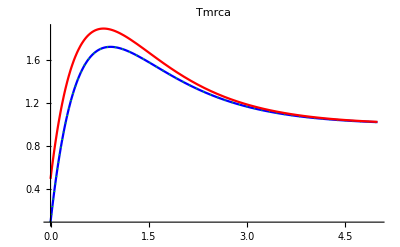

```mathematica
With[{Td=.1,Te=2, y = 2},
Block[{scaled = Log[(ⅇ^Td (-1-2 Te y+2 ⅇ^α Te y))/(-1-2 Te+2 ⅇ^α Te)],scalednoAlpha = Log[(ⅇ^Td (-1-2 Te y))/(-1-2 Te)]},
Show[
Plot[{TmrcaAI[α,Td,Te],TmrcaAI[α,scaled,Te y],TmrcaAI[α,scalednoAlpha,Te y]},{α,0,5},PlotStyle->{{Blue},{Green,Dotted},Red,Black},PlotRange->Full],PlotLabel->"Tmrca"
]
]
]
```

By allowing Td to rescale as a function of alpha, we correctly estimate the Tmrca (dashed green lines match the blue line in the plot above).  However, even this rescaling does not correctly recover the underlying distribution of Tmrca along the genome.  The distribution of Tmrca is well approximated with the rescaling factory both very near the sweep target and relatively far from the sweep target (α = 0.01 and α = 3, below). However, in the region flanking the sweep target, we can clearly distinguish the effects of the time since the sweep Td=Ta and the divergence of the donor at the time of introgression Te = Ts - Ta.

The reason is simple. As we saw in the marginal distribution  and point mass (above), the burst of coalesence depends only on Ta, while the split time Ts determines how far pastward the probability mass is shifted relative to the classic sweep (Where Ts -> Ta).

```mathematica
tplot[TaIncrement_,Ts_,α_]:=GraphicsColumn[{
Plot[
Evaluate[
Table[ fT1[T,TaIncrement*i,Ts-TaIncrement*i,α],{i,0,4}]],{T,0,15},PlotRange->Full,Exclusions->Full,PlotLabel->"α= "<>ToString[α]],
}
]; 
tplotScaled[TaIncrement_,Ts_,α_,y_]:=GraphicsColumn[{
Plot[
Evaluate[
Table[ fT1[T,Log[(ⅇ^(i TaIncrement) (-1-2 (-i TaIncrement+Ts) y+2 ⅇ^α (-i TaIncrement+Ts) y))/(-1-2 (-i TaIncrement+Ts)+2 ⅇ^α (-i TaIncrement+Ts))],Ts*y-TaIncrement*i,α],{i,0,4}]],{T,0,15},PlotRange->Full,Exclusions->Full,PlotLabel->"α= "<>ToString[α]]
}
]; 
GraphicsRow[
GraphicsColumn[ {tplot[.25,2,#],tplotScaled[.25,2,#,2]},Spacings->0]&/@{.01,.1,1,3},Spacings->0,ImageSize->Full
]
```

-Graphics-

## n=4: marginals with Yule and Star Compared

For the analysis, we parameterize by the inter - event times Td = Ta and Te = Ts - Ta.  If needed, we later substitute to recover as functions of Ts and Ta.

### starlike: AI vs Classic

```mathematica
gfDeltaEpsilonStar = GFaiStar[α,ω,{{1},{1},{1},{1}},δ,ϵ]//Expand;
gfDeltaEpsilonStar[[0]] = List;
gfDeltaEpsilonStar = gfDeltaEpsilonStar//.subAllPeeToOne[4]//.subAllPeeToEpsilon[4];
```

The expressions become complicated, so we obtain the marginal iTon branch type means, pdfs, and cdfs below without printing them.

```mathematica
meansList = MakeMeanList[gfDeltaEpsilonStar,4,ω,t,δ,Td,ϵ,Te];
pdfsList = MakePDFList[gfDeltaEpsilonStar,4,ω,t,δ,Td,ϵ,Te];
cdfsList = MakeCDFList[gfDeltaEpsilonStar,4,ω,t,δ,Td,ϵ,Te];
```

```mathematica
funMeans = Function[{α,Td,Te},Evaluate[#/.P->PknToAlpha]]&/@meansList;
funPdfs = Function[{t,α,Td,Te},Evaluate[#/.P->PknToAlpha]]&/@pdfsList;
funCdfs = Function[{t,α,Td,Te},Evaluate[#/.P->PknToAlpha]]&/@cdfsList;
```

Very near and very far from the sweep center, the marginal branch length distributions for the adaptive introgression case (solid lines: 1-Ton = blue, 2-Ton = green, 3-Ton = red)  are similar to the classic hard sweep case (dashed lines).  However, at intermediate distances from the sweep center, the coalescence times for the AI model are shifted pastward relative to those of the classic sweep.

```mathematica
tplot[α_,Tai_,Tsp_,Tlim_,funPdfs_,funCdfs_]:=GraphicsColumn[{
Show[
Plot[
Evaluate[#[T,α,Tai,Tsp-Tai]&/@funPdfs],{T,0,Tlim},PlotRange->Full,Exclusions->None,PlotStyle->{Blue,Green,Red},PlotLabel->"α= "<>ToString[α],ImageSize->Medium
],
Plot[
Evaluate[#[T,α,Tai,0]&/@funPdfs],{T,0,Tlim},PlotRange->Full,Exclusions->None,PlotStyle->Evaluate[{Dashed,Lighter[#]}&/@{Blue,Green,Red}]
]],
Show[
Plot[
Evaluate[#[T,α,Tai,Tsp-Tai ]&/@funCdfs],{T,0,Tlim},PlotRange->Full,Exclusions->None,PlotStyle->{Blue,Green,Red},PlotLabel->"α= "<>ToString[α],ImageSize->Medium
],
Plot[
Evaluate[#[T,α,Tai,0]&/@funCdfs],{T,0,Tlim},PlotRange->Full,Exclusions->None,PlotStyle->Evaluate[{Dashed,Lighter[#]}&/@{Blue,Green,Red}]
]]
},ImageSize->Medium]
Print["Ta = 0.01, Ts = 2"]
GraphicsRow[{
tplot[.01,.01,2,4,funPdfs,funCdfs],
tplot[.1,.01,2,4,funPdfs,funCdfs],
tplot[1,.01,2,4,funPdfs,funCdfs],
tplot[3,.01,2,4,funPdfs,funCdfs],
tplot[10,.01,2,4,funPdfs,funCdfs]
},ImageSize->Full]
Print["Ta = 0.1, Ts = 2"]
GraphicsRow[{
tplot[.01,.1,2,4,funPdfs,funCdfs],
tplot[.1,.1,2,4,funPdfs,funCdfs],
tplot[1,.1,2,4,funPdfs,funCdfs],
tplot[3,.1,2,4,funPdfs,funCdfs],
tplot[10,.1,2,4,funPdfs,funCdfs]
},ImageSize->Full]
```

Ta = 0.01, Ts = 2

-Graphics-

Ta = 0.1, Ts = 2

-Graphics-

For singleton and doubleton lineages, a point-mass can only be generated by selection. Singletons can all coalesce in a single burst if the first event is the selective sweep and none of the lineages escape.  Similarly, a point mass at t=0 results from a multiple merger of only 3 inidividuals. The size of these point masses depends only on Ta and the distance from the sweep target.  However, for tripleton lineages, the size of the pointmass at t=0 also depends on the time since the split Ts, and this is due to the structure imposed on the coalescent by the strict isolation model. For example,  suppose the sweep is the first event, and three out of four lineages escape. If the subsequent time to the population split is large, we expect all three of the escaped lineages to coalesce before coalescing with the donor lineage. In other words, for this sequence of events, the probability of observing tripleton-type branches is higher than under the classic sweep model due to the divergence time.

```mathematica
GetJumps[pdfsList,cdfsList,t]/.Td->Ta /.Te->Ts-Ta //FullSimplify
```

{{1,{HeavisideTheta[t-4 Ta],HeavisideTheta[t-2 Ta],HeavisideTheta[t-Ta],DiracDelta[t-4 Ta],HeavisideTheta[t-3 Ta-Ts],HeavisideTheta[t-Ta-Ts],HeavisideTheta[t-Ts],HeavisideTheta[t-2 (Ta+Ts)],HeavisideTheta[t-2 Ts],HeavisideTheta[t-4 Ts],HeavisideTheta[t-4 Ts]},{{t-4 Ta,ⅇ^(-6 Ta) P[0,4]}}},{2,{HeavisideTheta[t-Ta],HeavisideTheta[t-2 Ta],DiracDelta[t],HeavisideTheta[t+2 Ta-2 Ts],HeavisideTheta[t+Ta-2 Ts],HeavisideTheta[t-2 Ts],HeavisideTheta[t+Ta-Ts],HeavisideTheta[t-Ts]},{{t,ⅇ^(-6 Ta) (P[0,4]+P[1,4])}}},{3,{DiracDelta[t],HeavisideTheta[t-Ta],HeavisideTheta[t+Ta-Ts],HeavisideTheta[t-Ts]},{{t,1/6 ⅇ^(-3 (Ta+Ts)) (-P[3,4]+ⅇ^(-2 Ta+2 Ts) (-4 P[2,4]+3 P[3,4]+2 ⅇ^(-Ta+Ts) (-1+ⅇ^(6 Ta)-4 P[0,3]+4 ⅇ^(3 Ta) P[0,3]+3 P[0,4]+3 P[2,4]+P[4,4])))}}}}

### Instant Yule

```mathematica
sample= Table[{1},{i,1,4}];
substitute[allpees_List]:=Total[δ*Peln[#[[1]],#[[2]],Total[#],s,r,Ne,M]&/@allpees]->δ;
allFs=Table[partitions[i],{i,2,Length[sample]}];
substituteL=substitute/@allFs;
(*addition to sum probabilities to right value*)
(*substituteL=#->sumP[#[[1,2,3]]]*δ&/@substituteL*)

substituteL
```

{δ Peln[0,0,2,s,r,Ne,M]+δ Peln[0,1,2,s,r,Ne,M]+δ Peln[0,2,2,s,r,Ne,M]+δ Peln[1,0,2,s,r,Ne,M]+δ Peln[1,1,2,s,r,Ne,M]+δ Peln[2,0,2,s,r,Ne,M]→δ,δ Peln[0,0,3,s,r,Ne,M]+δ Peln[0,1,3,s,r,Ne,M]+δ Peln[0,2,3,s,r,Ne,M]+δ Peln[0,3,3,s,r,Ne,M]+δ Peln[1,0,3,s,r,Ne,M]+δ Peln[1,1,3,s,r,Ne,M]+δ Peln[1,2,3,s,r,Ne,M]+δ Peln[2,0,3,s,r,Ne,M]+δ Peln[2,1,3,s,r,Ne,M]+δ Peln[3,0,3,s,r,Ne,M]→δ,δ Peln[0,0,4,s,r,Ne,M]+δ Peln[0,1,4,s,r,Ne,M]+δ Peln[0,2,4,s,r,Ne,M]+δ Peln[0,3,4,s,r,Ne,M]+δ Peln[0,4,4,s,r,Ne,M]+δ Peln[1,0,4,s,r,Ne,M]+δ Peln[1,1,4,s,r,Ne,M]+δ Peln[1,2,4,s,r,Ne,M]+δ Peln[1,3,4,s,r,Ne,M]+δ Peln[2,0,4,s,r,Ne,M]+δ Peln[2,1,4,s,r,Ne,M]+δ Peln[2,2,4,s,r,Ne,M]+δ Peln[3,0,4,s,r,Ne,M]+δ Peln[3,1,4,s,r,Ne,M]+δ Peln[4,0,4,s,r,Ne,M]→δ}

```mathematica
gfDeltaListYule = Expand [ GFaiYule[s,r,Ne,M,ω,sample,{δ, ϵ}] ];
gfDeltaListYule⟦0⟧ = List;
gfDeltaListYule = gfDeltaListYule//.substituteL;
```

```mathematica
yulePDFS = MakeMargeList[gfDeltaListYule,sample,ω,t,δ,Td,ϵ,Te];
yulePDFS = Total[#]&/@yulePDFS;
```

```mathematica
yuleCDFS = MakeCumuList[gfDeltaListYule,sample,ω,t,δ,Td,ϵ,Te];
yuleCDFS = Total[#]&/@yuleCDFS;
```

### Data & Approximation Comparison

```mathematica
localPath = SetDirectory[NotebookDirectory[]]
pathToSims = "/simulations/ai_marginals/"
```

### Data & Approximation Comparison

```mathematica
recpersite= 1.*10^-6;
winDist = 100;
datNe = 10000;
shape = {10000,250,3}; (* {dataPoints,recPoints,infoCols}*)
```

```mathematica
sweepTimes={0,.1,.25,.5,1.0,1.5,2.0}*datNe
```

{0,1000.,2500.,5000.,10000.,15000.,20000.}

```mathematica
localPath = SetDirectory[NotebookDirectory[]];
pathToSims =localPath<> "/simulations/ai_marginals/";
dataFiles ={"np_s4_0.dat","np_s4_5000.dat","np_s4_10000.dat","np_s4_15000.dat","np_s4_17500.dat","np_s4_19000.dat","np_s4_20000.dat"};
dataFiles=Reverse[dataFiles]; (*do this because the times listed in the fiels are ms times not sample times, their reverse order matches the sweep times*)
dataFiles = pathToSims<>#&/@dataFiles
```

{/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/ai_marginals/np_s4_20000.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/ai_marginals/np_s4_19000.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/ai_marginals/np_s4_17500.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/ai_marginals/np_s4_15000.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/ai_marginals/np_s4_10000.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/ai_marginals/np_s4_5000.dat,/home/derek/Dropbox/projects/selection/ms_notebooks/simulations/ai_marginals/np_s4_0.dat}

```mathematica
allData = MapThread[MakeDataArray[#1,#2,shape,datNe]&,{sweepTimes,dataFiles}];
```

```mathematica
plt0[idxT_,idxr_,ss_,nn_,Tai_,Tdonor_]:=Module[ 
{rec = recpersite*idxr*winDist,m=Floor[2 nn 2 ss],Ta=Tai,Ts=Tdonor,α},
α = rec/ss Log[2 nn ss];
Show[
Plot[Evaluate[yulePDFS/.{s->ss,r->rec,Ne->nn,M->m,Td->Ta,Te->Ts}/.Peln->PELN],{t,0,3},PlotStyle->Evaluate[Darker[#]&/@{Blue,Green,Red}],Exclusions->None,PlotRange->Full],
Plot[Evaluate[#[t,α,Ta,Ts]&/@funPdfs],{t,0,3},PlotRange->Full,PlotStyle->Evaluate[{Darker[#],Dashed}&/@{Blue,Green,Red}],Exclusions->None],
Histogram[allData[[idxT]][[idxr]][[2]],{.05},"PDF",ChartStyle->Evaluate[Lighter[#]&/@{Blue,Green,Red}]
],
PlotLabel->"α= "<>ToString[α]<>"  Ta= "<>ToString[Ta],
PlotRange->{{0,3},{0,2}}
]
]
```

```mathematica
plt1[idxT_,idxr_,ss_,nn_,Tai_,Tdonor_]:=Module[ 
{rec = recpersite*idxr*winDist,m=Floor[2 nn 2 ss],Ta=Tai,Ts=Tdonor,α},
α = rec/ss Log[2 nn ss];
Show[
Plot[Evaluate[yuleCDFS/.{s->ss,r->rec,Ne->nn,M->m,Td->Ta,Te->Ts}/.Peln->PELN],{t,0,3},PlotStyle->Evaluate[Darker[#]&/@{Blue,Green,Red}],Exclusions->None,PlotRange->Full],
Plot[Evaluate[#[t,α,Ta,Ts]&/@funCdfs],{t,0,3},PlotRange->Full,PlotStyle->Evaluate[{Darker[#],Dashed}&/@{Blue,Green,Red}],Exclusions->None],
Histogram[allData[[idxT]][[idxr]][[2]],{.05},"CDF",ChartStyle->Evaluate[Lighter[#]&/@{Blue,Green,Red}]
],
PlotLabel->"α= "<>ToString[α]<>"  Ta= "<>ToString[Ta],
PlotRange->{{0,3},{0,1}}
]
]
```

```mathematica
(*sampleTimeIndexes = {2, 4, 5, 7};
distanceIndexes = {3, 11, 51, 101};*)
sampleTimeIndexes = {2, 4};
distanceIndexes = { 11, 51};
```

```mathematica
sampleTimeIndexes = {1,3,5,7};
distanceIndexes = {2,10,50,100};
```

For the classic hard sweep scenario, there is very little improvement in the accuracy of the analytic results using the Yule approximation despite a substantial increase in computation costs. Despite only minor differences, we observed more accurate parameter estimation using the Yule approximation for the classic sweep scenario.   For the adaptive introgression scenario, however, the Yule approximation does provide a clearly better fit for the marginal distributions, particularly at intermediate recombination distances where lineages  have the highest probability of being separated during the time prior to the sweep and before the split of the ancestral population (this is easiest to see in the CDFs). The Yule approximation is likely more useful when estimating parameters under models with more complex demography.

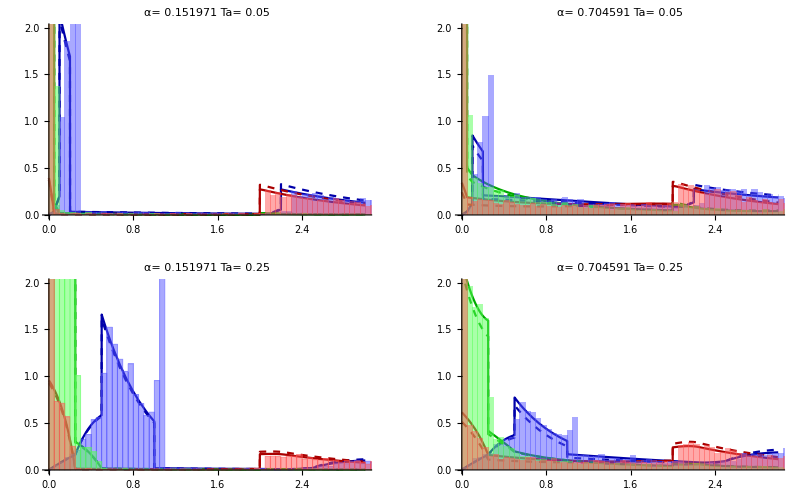

```mathematica
GraphicsGrid[
Table[
Table[
plt0[tIdx,rIdx,.05,datNe,sweepTimes[[tIdx]]/(2*datNe),2.0],{rIdx,distanceIndexes}],{tIdx,sampleTimeIndexes}]
]
```

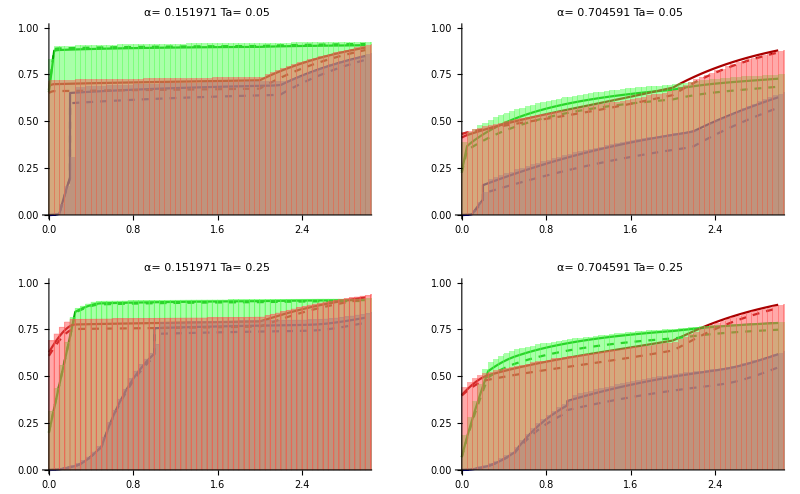

```mathematica
GraphicsGrid[
Table[
Table[
plt1[tIdx,rIdx,.05,datNe,sweepTimes[[tIdx]]/(2*datNe),2.0],{rIdx,distanceIndexes}],{tIdx,sampleTimeIndexes}]
]
```

## Site Frequency Spectrum

Here we derive the SFS, analgous to the calssic hard sweep scenario of the main text.  The GF as a list and the mean length of iton branches have been pre-computed.

```mathematica
(*n=8;
gfStarList = Block[{sample = Table[{1},{i,1,n}],gfDeltaEpsilon},
gfDeltaEpsilon =GFaiStar[α,ω,sample,δ,ϵ] //Expand;
gfDeltaEpsilon[[0]] = List;
gfDeltaEpsilon = SubSimplifyPeeRulesv2[#,n]&/@gfDeltaEpsilon//Parallelize;
gfDeltaEpsilon];

meansList = MakeMeanList[gfStarList,n,ω,t,δ,Ta,ϵ,Ts];
meanItonFunList = Function[{α,Ta,Ts},Evaluate[#//.P->PknToAlpha/.{Td->Ta,Te->Ts}]]&/@meansList;
sfs[α_,Ta_,Ts_]:=Block[{a = #[α,Ta,Ts]&/@meanItonFunList},a/Total[a]]*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*DumpSave["ai_iTonBL_8_gfStarList_meansList.mx",{gfStarList,meansList}]*)
Get["ai_iTonBL_8_gfStarList_meansList.mx"]
meanItonFunList = Function[{α,Ta,Ts},Evaluate[#//.P->PknToAlpha/.{Td->Ta,Te->Ts}]]&/@meansList;
sfs[α_,Ta_,Ts_]:=Block[{a = #[α,Ta,Ts]&/@meanItonFunList},a/Total[a]]
```

```mathematica
sfs[.1,.2,3]
```

{0.396556,0.150744,0.0763606,0.0549814,0.0639682,0.0983329,0.159057}

{α= 0,α= 0.25,α= 0.75,α= 1.5}

{α= 0,α= 0.25,α= 0.75,α= 1.5}

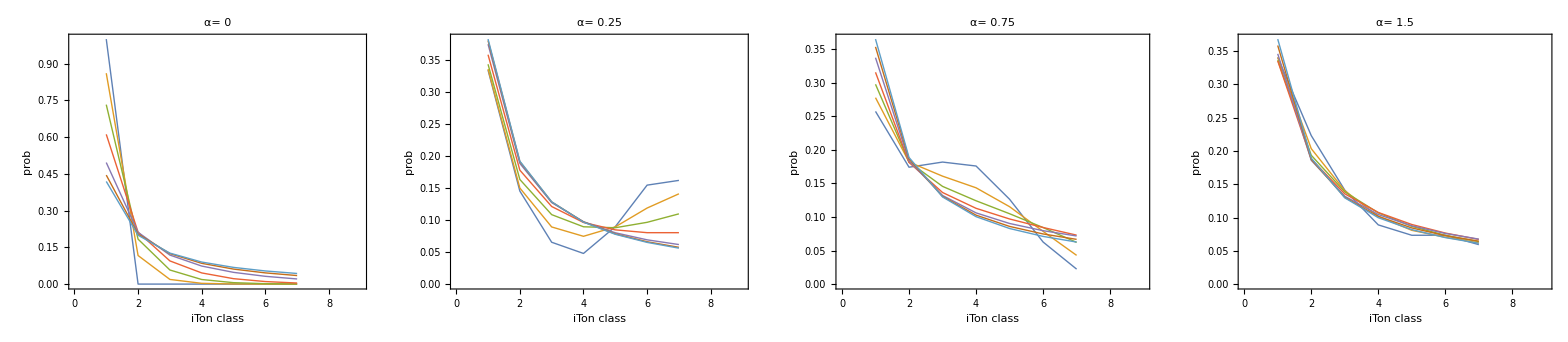

```mathematica
(*tslist = {0.000001,.5,1,1.5,2,2.5};*)
tslist = {0.00000001,.1,.25,.5,1,1.5,2};
alphaList = {0,0.25,0.5};
legendItems = "Ts= "<>ToString[#]&/@{0,.1,.25,.5,1,1.5,2};
titleItems = "α= "<>ToString[#]&/@{0,.25,.75,1.5}

(*plt1 = getSFS[expectedBLs,0,#]&/@tslist;
plt2 = getSFS[expectedBLs,0.25,#]&/@tslist;
plt3 = getSFS[expectedBLs,0.75,#]&/@tslist;*)
plt1 = sfs[0,#,2.0]&/@tslist;
plt2 = sfs[0.25,#,2.0]&/@tslist;
plt3 = sfs[0.75,#,2.0]&/@tslist;
plt4 = sfs[1.5,#,2.0]&/@tslist;
pltFull = GraphicsRow[
MapThread[ 
ListPlot[#1,Joined->True,PlotRange->{{0,9},All},Frame->{{True,False},{True,False}},FrameLabel->{"iTon class","prob"},FrameStyle->Directive[Thick,Black,Bold,12],LabelStyle->Directive[12,Bold,Black],PlotStyle->Directive[12,Bold,Thick],
(*PlotLegends->SwatchLegend[legendItems],*)
PlotLabel->#2]&,{{plt1,plt2,plt3,plt4},titleItems}
],
Spacings->0,ImageSize->Full
];
pltFull
```